## Random walks in the plane, four directions

make a random choice of direction

```mathematica
g:=RandomChoice[{{0,1},{0,-1},{1,0},{-1,0}}]
```

the function step1 takes as input an (integer) point in the plane and steps in one of 4 directions, randomly chosen using g, of a step length 1:

```mathematica
step1[x_]:=x+g
```

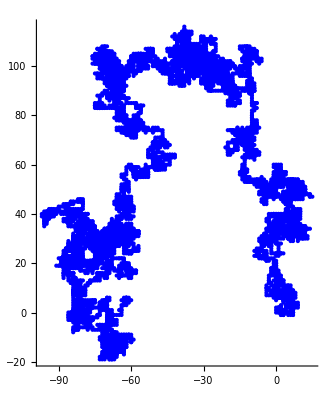

```mathematica
Graphics[{PointSize[Small],Blue,NestList[step1,{0,0},10000]//Point},Axes->True]
```

```mathematica
step2[x_]:=Module[{g=RandomChoice[{{0,1},{0,-1},{1,0},{-1,0}}]},
If[Norm[x+g]≤10,x+g,10(x+g)/Norm[x+g]]
]
```

```mathematica
findAngle[{a_,b_}]:=Arg[a+I b]
```

```mathematica
step3[x_]:=Module[{g,θ},
g=RandomChoice[{{0,1},{0,-1},{1,0},{-1,0}}];
If[Norm[x+g]≤10,x+g,θ=findAngle[x+g];x+g-{Cos[θ],Sin[θ]}]
]
```

```mathematica
step3[{0,0}]
```

{0,-1}

start at the point {0,0} and do some number of steps, returning a list of these poiunts (the random walk):

```mathematica
NestList[step3,{0.0,0.0},50]
```

{{0.,0.},{0.,-1.},{0.,-2.},{0.,-3.},{0.,-2.},{0.,-1.},{0.,-2.},{0.,-3.},{0.,-2.},{1.,-2.},{2.,-2.},{3.,-2.},{2.,-2.},{3.,-2.},{3.,-3.},{3.,-4.},{3.,-5.},{4.,-5.},{4.,-6.},{4.,-5.},{4.,-6.},{4.,-5.},{4.,-6.},{4.,-7.},{4.,-8.},{5.,-8.},{4.51436,-8.12584},{4.51436,-7.12584},{3.51436,-7.12584},{4.51436,-7.12584},{5.51436,-7.12584},{6.51436,-7.12584},{5.51436,-7.12584},{4.51436,-7.12584},{4.51436,-8.12584},{5.51436,-8.12584},{4.99718,-8.26996},{4.99718,-7.26996},{4.99718,-6.26996},{4.99718,-5.26996},{4.99718,-4.26996},{5.99718,-4.26996},{5.99718,-3.26996},{6.99718,-3.26996},{7.99718,-3.26996},{6.99718,-3.26996},{6.99718,-2.26996},{5.99718,-2.26996},{5.99718,-3.26996},{5.99718,-4.26996},{5.99718,-3.26996}}

```mathematica
NestList[step3,{0.0,0.0},50]
```

{{0.,0.},{0.,1.},{-1.,1.},{-1.,0.},{-1.,1.},{-1.,2.},{-1.,1.},{-2.,1.},{-2.,2.},{-2.,3.},{-3.,3.},{-3.,2.},{-3.,1.},{-2.,1.},{-2.,0.},{-3.,0.},{-4.,0.},{-3.,0.},{-2.,0.},{-3.,0.},{-4.,0.},{-5.,0.},{-6.,0.},{-7.,0.},{-6.,0.},{-6.,-1.},{-5.,-1.},{-4.,-1.},{-3.,-1.},{-4.,-1.},{-4.,-2.},{-4.,-1.},{-4.,0.},{-5.,0.},{-6.,0.},{-7.,0.},{-7.,1.},{-8.,1.},{-9.,1.},{-8.,1.},{-8.,2.},{-8.,3.},{-9.,3.},{-9.,4.},{-9.07152,3.62861},{-9.07152,2.62861},{-9.10394,2.37607},{-9.13049,2.14716},{-9.13049,1.14716},{-9.13049,2.14716},{-8.13049,2.14716}}

apply Point to these points and plot as graphics primitives::

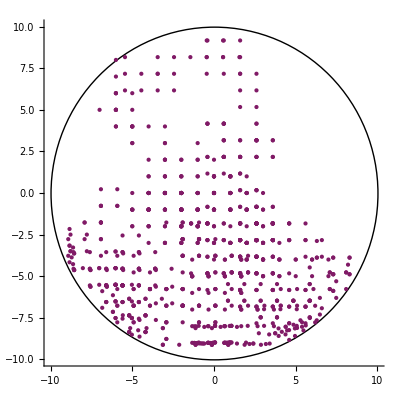

```mathematica
Graphics[{Circle[{0,0},10],PointSize[Medium],RGBColor[0.5,0.1,0.4],NestList[step3,{0.0,0.0},1000]//Point},Axes->True]
```

the next command only gives the end point of a random walk of 5000 steps:

```mathematica
NestList[step1,{0,0},10]
```

{{0,0},{-1,0},{-1,1},{0,1},{1,1},{1,2},{1,1},{1,0},{2,0},{3,0},{4,0}}

## Here we use NestWhile command to find total steps takes to hit the gate

```mathematica
findAngle[{a_,b_}]:=Arg[a+I b]
```

```mathematica
step3[x_]:=Module[{g,θ},
g=RandomChoice[{{0,1},{0,-1},{1,0},{-1,0}}];
If[Norm[x+g]≤10,x+g,θ=findAngle[x+g];x+g-{Cos[θ],Sin[θ]}]
]
```

```mathematica
NestWhile[step3,{10,10},(Norm[#]>10Or Abs[findAngle[#]]>Pi/8)&]
```

{10,10}

### Questions: The NestWhile Command does not work

the next command does 10 random walks of length 5000 steps, creating a list of the 10 ending points:

```mathematica
Table[Nest[step1,{0,0},5000],{10}]
```

{{-33,23},{-72,-10},{3,27},{82,62},{30,78},{36,52},{64,2},{86,-6},{61,-73},{16,44}}

here we do 1000 random walks and plot of the final points:

```mathematica
Graphics[{PointSize[Small],Red,Point[tmp=Table[Nest[step3,{0.0,0.0},5000],{500}]]},Axes->True]
```

$Aborted

```mathematica
$Aborted
```

$Aborted

here is a histogram of the distances of the above points to the origin:

```mathematica
Histogram[Norm/@tmp]
```

Histogram::ldata: tmp is not a valid dataset or list of datasets.

Histogram[tmp]

```mathematica
ratio[{a_,b_}]:=b/a
```

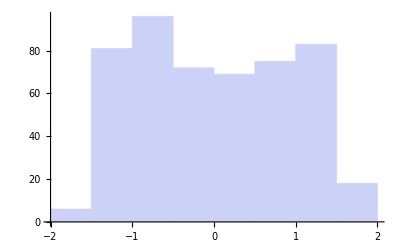

```mathematica
Histogram[ArcTan[ratio/@tmp]]
```

### Sandbox

```mathematica
findAngle[{0,1}]
```

π/2

```mathematica
h[6]
```

15

```mathematica
a
```

3

```mathematica
Count[Module[{g=RandomChoice[{{0,1},{0,-1},{1,0},{-1,0}}]},
If[Norm[x+g]<10,x+g,10(x+g)/Norm[x+g]]
],Norm[x+g]>10]
```

0